# 4.2)

#### a)

```mathematica
(*The answer is derived by paper and pen, so it is attached in a seperate file in OpenTa*)
Dq[q_]:=1/(1-q)*Log[(2/3)^q + (1/3)^q]/Log[3];
Dq[q]
```

Log[(2/3)^q+3^-q]/((1-q) Log[3])

#### b)

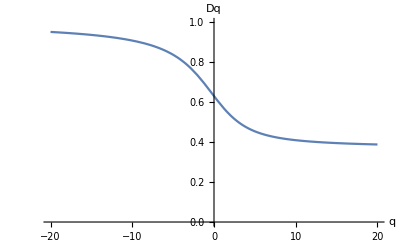

```mathematica
DqPlot = Plot[Dq[q],{q,-20,20}];
Show[DqPlot,AxesLabel->{"q","Dq"},PlotRange->{{-20,20},{0,1}},AxesOrigin->{0,0}]
```

#### c)

```mathematica
(*Just put in the values for q, so q=1 and q=2! Need limit for q=1 otherwise it will be zero in the denominator*)
D1=Limit[Dq[q],q->1]
D2 = Dq[2]
```

Log[27/4]/Log[27]

Log[9/5]/Log[3]

#### d)

```mathematica
(*Just make the q go to infinity and in the other case -infinity*)
DInf = Limit[Dq[q],q->Infinity]
DNegativeInf = Limit[Dq[q],q->-Infinity]
```

Log[3/2]/Log[3]

1